### Building the SIR model

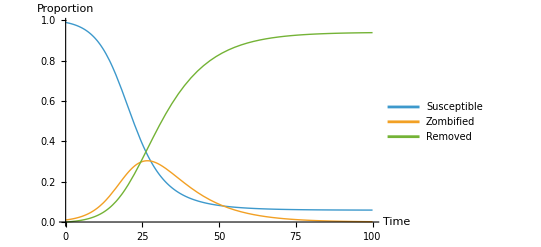

```mathematica
ClearAll[S, Z, R, t, beta, gamma];

(*Define the variables*)
beta = 0.3;
gamma = 0.1;

sirEquations = {
S'[t] == -beta S[t] Z[t],
Z'[t] == beta S[t] Z[t] - gamma Z[t],
R'[t] == gamma Z[t],
S[0] == 0.99,
Z[0] ==  0.01,
R[0] == 0
};

sirSolution = NDSolve[sirEquations, {S, Z, R}, {t, 0, 100}];

Plot[
Evaluate[{S[t], Z[t], R[t]} /. sirSolution],
{t, 0, 100},
PlotLegends->{"Susceptible", "Zombified", "Removed"},
AxesLabel-> {"Time", "Proportion"},
PlotRange -> All,
PlotStyle -> Thick
]
```

### Building a predator prey model

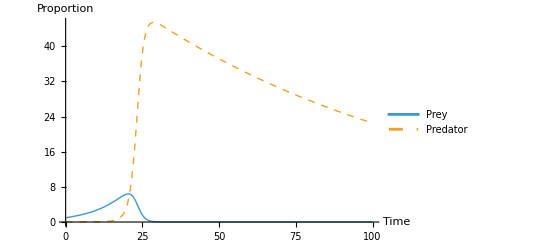

```mathematica
ClearAll[prey,predator,a,b,c,d,t];

(* Define the parameters for the predator-prey model *)
a=0.1; (* Growth rate of prey *)
b=0.02; (* Predation rate coefficient *)
c=0.1; (* Natural death rate of predators *)
d=0.01; (* Rate at which predators increase by consuming prey *)

(* Define the Lotka-Volterra equations *)
predatorPreyEquations={
    prey'[t]==a prey[t]-b prey[t] predator[t],
    predator'[t]==c prey[t] predator[t]-d predator[t],
    prey[0]==0.99,
    predator[0]==0.01
};

(* Solve the predator-prey system *)
predatorPreySolution=NDSolve[
    {prey'[t]==a prey[t]-b prey[t] predator[t],
     predator'[t]==c prey[t] predator[t]-d predator[t],
     prey[0]==0.99,
     predator[0]==0.01},
    {prey,predator},{t,0,100}
];

(* Plot the result *)
Plot[
    Evaluate[{prey[t],predator[t]} /. predatorPreySolution],
    {t,0,100},
    PlotLegends->{"Prey","Predator"},
    AxesLabel->{"Time","Proportion"},
    PlotRange->All,
    PlotStyle->{Thick,{Dashed,Thick}}
]
```

### Unifying the SIR and predator prey model

```mathematica
ClearAll[S,Z,R,prey,predator,a,b,c,d,beta,gamma,t];

(* Parameters for SIR model *)
beta=0.3; (* Infection rate *)
gamma=0.1; (* Recovery rate *)

(* Parameters for predator-prey model *)
a=0.1; (* Growth rate of prey *)
b=0.02; (* Predation rate coefficient *)
c=0.1; (* Natural death rate of predators *)
d=0.01; (* Rate at which predators increase by consuming prey *)

(* Define interactions between models *)
interactionRate=0.01; (* Example interaction rate *)

(* Combined differential equations *)
combinedEquations={
  S'[t]==-beta S[t] Z[t],
  Z'[t]==beta S[t] Z[t]-gamma Z[t],
  R'[t]==gamma Z[t],
  
  prey'[t]==c prey[t]-b prey[t] predator[t]-interactionRate Z[t] prey[t],
  predator'[t]==c prey[t] predator[t]-d predator[t],
  
  S[0]==0.99,
  Z[0]==0.01,
  R[0]==0,
  prey[0]==0.99,
  predator[0]==0.01
};

(* Solve the system *)
solution=NDSolve[combinedEquations,{S,Z,R,prey,predator},{t,0,100}];

(* Plot the results *)
sirPlot =
  Plot[
    Evaluate[{S[t], Z[t], R[t]} /. solution],
    {t, 0, 100},
    PlotLegends -> {"Susceptible", "Infected", "Recovered"},
    Frame -> True, FrameLabel -> {"Time", "Proportion"},
    PlotRange -> All, PlotStyle -> Thick, ImageSize -> 450
  ];

(* Ecology plot (absolute units) *)
ecoPlot =
  Plot[
    Evaluate[{prey[t], predator[t]} /. solution],
    {t, 0, 100},
    PlotLegends -> {"Prey", "Predator"},
    Frame -> True, FrameLabel -> {"Time", "Population (arb. units)"},
    PlotRange -> All, PlotStyle -> {Thick, {Thick, Dashed}}, ImageSize -> 450
  ];
  
GraphicsRow[{sirPlot, ecoPlot}, Spacings -> Scaled[.6], ImageSize -> 950]
```

-Graphics-

### Making the model able to be manipulated

```mathematica
ClearAll[S,Z,R,prey,predator,t];

Manipulate[
Module[
{equations,solution,betaEff,gammaEff,r0},
(*BOUNDED couplings:always positive,saturating effects*)
betaEff[t_]:=beta/(1+kBeta*prey[t]);(*more prey->smaller β,never≤0*)
gammaEff[t_]:=gamma*(1+kGamma*predator[t]/(1+predator[t]));(*more predators->larger γ,bounded*)

equations={
S'[t]==-betaEff[t] S[t] Z[t],
Z'[t]==betaEff[t] S[t] Z[t]-gammaEff[t] Z[t],
R'[t]==gammaEff[t] Z[t],

prey'[t]==a prey[t]-b prey[t] predator[t]-interactionRate Z[t] prey[t],
predator'[t]==c prey[t] predator[t]-d predator[t],

S[0]==0.99,
Z[0]==0.01,
R[0]==0,

prey[0]==0.99,
predator[0]==0.01};

solution=NDSolve[
equations,{S,Z,R,prey,predator},
{t,0,100},

Method->"StiffnessSwitching",
MaxStepFraction->1/500];

r0[t_]:=(betaEff[t] S[t])/gammaEff[t]/. solution;

(*instantaneous reproduction ratio*)

Column[
{
Plot[Evaluate[{S[t],Z[t],R[t]}/. solution],
{t,0,100},PlotLegends->{"Susceptible","Infected","Recovered"},
Frame->True,FrameLabel->{"Time","Proportion"},
PlotRange->All,PlotStyle->Thick,
PlotLabel->Style["SIR Dynamics",Bold,14]],

Plot[Evaluate[{prey[t],predator[t]}/. solution],
{t,0,100},PlotLegends->{"Prey","Predator"},
Frame->True,FrameLabel->{"Time","Population (arb. units)"},
PlotRange->All,PlotStyle->Thick,
PlotLabel->Style["Predator–Prey Dynamics",Bold,14]],

Show[Plot[r0[t],
{t,0,100},
Frame->True,FrameLabel->{"Time","R0(t)"},
PlotRange->All,PlotStyle->Thick,
PlotLabel->Style["Instantaneous R0(t)",Bold,14]],
Plot[1,{t,0,100},PlotStyle->{Dashed}]]}]],

(*----Sliders----*)
{{beta,0.30,"Base infection rate (β)"},0.01,1,Appearance->"Labeled"},
{{gamma,0.10,"Base recovery rate (γ)"},0.01,1,Appearance->"Labeled"},
{{a,0.10,"Prey growth rate (a)"},0.01,1,Appearance->"Labeled"},
{{b,0.02,"Predation rate (b)"},0.001,0.2,Appearance->"Labeled"},
{{c,0.10,"Predator growth per prey (c)"},0.01,1,Appearance->"Labeled"},
{{d,0.01,"Predator death (d)"},0.001,0.2,Appearance->"Labeled"},
{{interactionRate,0.01,"Zombie–prey interaction rate"},0,0.2,Appearance->"Labeled"},

Delimiter,
{{kBeta,0.3,"Prey effect on β (kBeta)"},0.,2.,Appearance->"Labeled"},
{{kGamma,0.5,"Predator effect on γ (kGamma)"},0.,2.,Appearance->"Labeled"}
]
```

### Implementing seasons

```mathematica
ClearAll[S,Z,R,prey,predator,t];

Manipulate[
Module[
{equations,solution,betaEff,gammaEff,r0,betaSeasonal,aSeasonal},

(*Seasonal variation*)
betaSeasonal[t_]:=beta*(1+Aβ*Sin[2*Pi*t/Tseason]);
aSeasonal[t_]:=a*(1+Aa*Sin[2*Pi*t/Tseason+phi]);

(*Bounded couplings:always positive,saturating effects*)
betaEff[t_]:=betaSeasonal[t]/(1+kBeta*prey[t]);
gammaEff[t_]:=gamma*(1+kGamma*predator[t]/(1+predator[t]));
equations={
S'[t]==-betaEff[t] S[t] Z[t],
Z'[t]==betaEff[t] S[t] Z[t]-gammaEff[t] Z[t],
R'[t]==gammaEff[t] Z[t],
prey'[t]==aSeasonal[t] prey[t]-b prey[t] predator[t]-interactionRate Z[t] prey[t],
predator'[t]==c prey[t] predator[t]-d predator[t],

S[0]==0.99,
Z[0]==0.01,
R[0]==0,
prey[0]==0.99,
predator[0]==0.01
};

solution=NDSolve[
equations,
{S,Z,R,prey,predator},
{t,0,100},
Method->"StiffnessSwitching",
MaxStepFraction->1/500];

r0[t_]:=(betaEff[t] S[t])/gammaEff[t]/. solution;

Column[
{Plot[
Evaluate[{S[t],Z[t],R[t]}/. solution],
{t,0,100},
PlotLegends->{"Susceptible","Infected","Recovered"},
Frame->True,
FrameLabel->{"Time","Proportion"},
PlotRange->All,
PlotStyle->Thick,
PlotLabel->Style["SIR Dynamics (with Seasons)",Bold,14]],

Plot[
Evaluate[{prey[t],predator[t]}/. solution],
{t,0,100},
PlotLegends->{"Prey","Predator"},
Frame->True,
FrameLabel->{"Time","Population (arb. units)"},
PlotRange->All,PlotStyle->Thick,
PlotLabel->Style["Predator–Prey Dynamics (with Seasons)",Bold,14]],

Show[
Plot[r0[t],
{t,0,100},
Frame->True,
FrameLabel->{"Time","R0(t)"},
PlotRange->All,PlotStyle->Thick,
PlotLabel->Style["Instantaneous R0(t)",Bold,14]],

Plot[1,
{t,0,100},PlotStyle->{Dashed}]]}]],

(*Sliders*)
{{beta,0.30,"Base infection rate (β)"},0.01,1},
{{gamma,0.10,"Base recovery rate (γ)"},0.01,1},
{{a,0.10,"Prey growth rate (a)"},0.01,1},
{{b,0.02,"Predation rate (b)"},0.001,0.2},
{{c,0.10,"Predator growth per prey (c)"},0.01,1},
{{d,0.01,"Predator death (d)"},0.001,0.2},
{{interactionRate,0.01,"Zombie–prey interaction rate"},0,0.2},

Delimiter,
{{kBeta,0.3,"Prey effect on β (kBeta)"},0.,2.},
{{kGamma,0.5,"Predator effect on γ (kGamma)"},0.,2.},

Delimiter,{{Aβ,0.3,"Seasonal amplitude on β"},0.,1.},
{{Aa,0.2,"Seasonal amplitude on a"},0.,1.},
{{Tseason,50,"Seasonal period (days)"},10,100},
{{phi,0,"Phase shift between β and a"},0,2*Pi}
]
```

#### Implementing zombie variants

```mathematica
ClearAll[S,Z1,Z2,Z3,R,prey,predator,t];

Manipulate[
Module[
{equations,solution,betaSeasonal,aSeasonal,betaEff,gammaEff,r0,Ztotal,w1=1,w2=1.2,w3=0.8}, (*weights for transmissibility*)

(*Seasonal variation*)
betaSeasonal[t_]:=beta*(1+Aβ*Sin[2*Pi*t/Tseason]);
aSeasonal[t_]:=a*(1+Aa*Sin[2*Pi*t/Tseason+phi]);

(*Shared couplings for all variants*)
betaEff[t_]:=betaSeasonal[t]/(1+kBeta*prey[t]);
gammaEff[t_]:=gamma*(1+kGamma*predator[t]/(1+predator[t]));

(*ODE system*)
equations={
S'[t]==-betaEff[t] S[t] (w1 Z1[t]+w2 Z2[t]+w3 Z3[t]),
Z1'[t]==betaEff[t] w1 S[t] Z1[t]-gammaEff[t] Z1[t],
Z2'[t]==betaEff[t] w2 S[t] Z2[t]-gammaEff[t] Z2[t],
Z3'[t]==betaEff[t] w3 S[t] Z3[t]-gammaEff[t] Z3[t],
R'[t]==gammaEff[t] (Z1[t]+Z2[t]+Z3[t]),

prey'[t]==aSeasonal[t] prey[t]-b prey[t] predator[t]-interactionRate (Z1[t]+Z2[t]+Z3[t]) prey[t],
predator'[t]==c prey[t] predator[t]-d predator[t],

(*Initial conditions*)
S[0]==0.99,
Z1[0]==0.005,
Z2[0]==0.003,
Z3[0]==0.002,
R[0]==0,
prey[0]==0.99,
predator[0]==0.01};

(*Solve system*)

solution=
NDSolve[
equations,
{S,Z1,Z2,Z3,R,prey,predator},
{t,0,100},
Method->"StiffnessSwitching",MaxStepFraction->1/500];

Ztotal[t_]:=Z1[t]+Z2[t]+Z3[t];
r0[t_]:=(betaEff[t] S[t])/gammaEff[t]/. solution;
Column[
{Plot[Evaluate[{S[t],Ztotal[t],R[t]}/. solution],
{t,0,100},
PlotLegends->{"Susceptible","Infected (total)","Recovered"},
Frame->True,
FrameLabel->{"Time","Proportion"},
PlotRange->All,PlotStyle->Thick,
PlotLabel->Style["SIR Dynamics (with 3 Zombie Variants)",Bold,14]],

Plot[Evaluate[{Z1[t],Z2[t],Z3[t]}/. solution],
{t,0,100},
PlotLegends->{"Variant 1","Variant 2","Variant 3"},
Frame->True,
FrameLabel->{"Time","Infected by Variant"},
PlotRange->All,
PlotStyle->Thick,
PlotLabel->Style["Individual Zombie Variants",Bold,14]],

Plot[Evaluate[{prey[t],predator[t]}/. solution],
{t,0,100},
PlotLegends->{"Prey","Predator"},
Frame->True,
FrameLabel->{"Time","Population (arb. units)"},
PlotRange->All,
PlotStyle->Thick,
PlotLabel->Style["Predator–Prey Dynamics (with Seasons)",Bold,14]],

Show[
Plot[r0[t],
{t,0,100},
Frame->True,
FrameLabel->{"Time","R0(t)"},
PlotRange->All,
PlotStyle->Thick,
PlotLabel->Style["Instantaneous R0(t)",Bold,14]],

Plot[1,{t,0,100},PlotStyle->{Dashed}
]
]
}
]
],

(*Sliders*)
{{beta,0.30,"Base infection rate (β)"},0.01,1},
{{gamma,0.10,"Base recovery rate (γ)"},0.01,1},
{{a,0.10,"Prey growth rate (a)"},0.01,1},
{{b,0.02,"Predation rate (b)"},0.001,0.2},
{{c,0.10,"Predator growth per prey (c)"},0.01,1},
{{d,0.01,"Predator death (d)"},0.001,0.2},
{{interactionRate,0.01,"Zombie–prey interaction rate"},0,0.2},

Delimiter,
{{kBeta,0.3,"Prey effect on β (kBeta)"},0.,2.},
{{kGamma,0.5,"Predator effect on γ (kGamma)"},0.,2.},

Delimiter,
{{Aβ,0.3,"Seasonal amplitude on β"},0.,1.},
{{Aa,0.2,"Seasonal amplitude on a"},0.,1.},
{{Tseason,50,"Seasonal period (days)"},10,100},
{{phi,0,"Phase shift between β and a"},0,2*Pi}
]
```

### Wrapping the core simulation in a callable function

```mathematica
ClearAll[simulateZombieSystem];

simulateZombieSystem[params_Association]:=
Module[
{beta=params["beta"],
gamma=params["gamma"],
a=params["a"],
b=params["b"],
c=params["c"],
d=params["d"],
interactionRate=params["interactionRate"],
kBeta=params["kBeta"],
kGamma=params["kGamma"],
Aβ=params["Aβ"],
Aa=params["Aa"],
Tseason=params["Tseason"],
phi=params["phi"],
w1=1,
w2=1.2,
w3=0.8,
betaSeasonal,
aSeasonal,
betaEff,
gammaEff,
equations,
solution
},

(*Seasonal effects*)
betaSeasonal[t_]:=beta*(1+Aβ*Sin[2*Pi*t/Tseason]);
aSeasonal[t_]:=a*(1+Aa*Sin[2*Pi*t/Tseason+phi]);

(*Coupling effects*)
betaEff[t_]:=betaSeasonal[t]/(1+kBeta*prey[t]);
gammaEff[t_]:=gamma*(1+kGamma*predator[t]/(1+predator[t]));
(*ODE system*)

equations={
S'[t]==-betaEff[t] S[t] (w1 Z1[t]+w2 Z2[t]+w3 Z3[t]),
Z1'[t]==betaEff[t] w1 S[t] Z1[t]-gammaEff[t] Z1[t],
Z2'[t]==betaEff[t] w2 S[t] Z2[t]-gammaEff[t] Z2[t],
Z3'[t]==betaEff[t] w3 S[t] Z3[t]-gammaEff[t] Z3[t],
R'[t]==gammaEff[t] (Z1[t]+Z2[t]+Z3[t]),
prey'[t]==aSeasonal[t] prey[t]-b prey[t] predator[t]-interactionRate (Z1[t]+Z2[t]+Z3[t]) prey[t],
predator'[t]==c prey[t] predator[t]-d predator[t],

(*Initial conditions*)
S[0]==0.99,
Z1[0]==0.005,
Z2[0]==0.003,
Z3[0]==0.002,
R[0]==0,
prey[0]==0.99,
predator[0]==0.01

};
(*Solve system*)

solution=NDSolve[
equations,
{S,Z1,Z2,Z3,R,prey,predator},
{t,0,100},
Method->"StiffnessSwitching"
];
(*Return rules so caller can extract functions*)
First[solution]];

(*---TEST PARAMETERS---*)
params=<|"beta"->0.3,"gamma"->0.1,"a"->0.1,"b"->0.02,"c"->0.05,"d"->0.05,"interactionRate"->0.01,"kBeta"->0.3,"kGamma"->0.5,"Aβ"->0.3,"Aa"->0.2,"Tseason"->50,"phi"->0|>;

(*---RUN CORE SYSTEM---*)
solRules=simulateZombieSystem[params];

(*Extract functions from rules*)
Sfun=S/. solRules;
Z1fun=Z1/. solRules;
Z2fun=Z2/. solRules;
Z3fun=Z3/. solRules;
Rfun=R/. solRules;
preyFun=prey/. solRules;
predFun=predator/. solRules;

ZtotalFun[t_]:=Z1fun[t]+Z2fun[t]+Z3fun[t];
```

## Dimensionless units group report

```mathematica
ClearAll[dimensionlessGroups];
dimensionlessGroups[params_Association]:=<|
"R0 (β/γ)"->params["beta"]/params["gamma"],
"α (a/γ)"->params["a"]/params["gamma"],
"δ (d/γ)"->params["d"]/params["gamma"],
"θ (c/γ)"->params["c"]/params["gamma"],
"β_pq (b/γ)"->params["b"]/params["gamma"],
"χ (interaction/γ)"->params["interactionRate"]/params["gamma"],
"T̃ (γ Tseason)"->params["gamma"]*params["Tseason"],
"kβ"->params["kBeta"],
"kγ"->params["kGamma"],
"Aβ"->params["Aβ"],
"Aa"->params["Aa"],
"ϕ"->params["phi"]|>;

Grid[Prepend[
Normal@KeyValueMap[{#1,NumberForm[#2,{6,3}]}&,dimensionlessGroups[params]],
{"Group","Value"}]
,Frame->All]
```

Group | Value
R0 (β/γ) | 3.000
α (a/γ) | 1.000
δ (d/γ) | 0.500
θ (c/γ) | 0.500
β_pq (b/γ) | 0.200
χ (interaction/γ) | 0.100
T̃ (γ Tseason) | 5.000
kβ | 0.300
kγ | 0.500
Aβ | 0.300
Aa | 0.200
ϕ | 0